```mathematica
<<MultivariateStatistics`
```

```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
history=Table[,{2},{90}];
```

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
window=90;window1=window+1;
```

```mathematica
For[h=0,h≤32,h++,
daysago=h;

returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window-daysago,-1-daysago}];
returnsr=Table[Log[closer[[a,b-1]]/closer[[a,b]]],{a,51},{b,-window-daysago,-1-daysago}];
cvard=Table[,{51},{51}];cvarr=Table[,{51},{51}];
For[d=1,d≤51,d++,
For[c=1, c≤51, c++, cvard[[d,c]]=Covariance[returnsd[[c]],returnsd[[d]] ];
cvarr[[d,c]]=Covariance[returnsr[[c]],returnsr[[d]] ]
]];
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]+daysago;
closed2=Table[closed[[e,-window-daysago;;-1-daysago]],{e,51}];
closer2=Table[closer[[f,-window-daysago;;-1-daysago]],{f,51}];
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr],timeleft]]];
endd=closed2[[All,-1]];
endr=closer2[[All,-1]];
For[g=1,g≤51,g++,Do[endd[[g]]=endd[[g]] ds[[g,z]];endr[[g]]=endr[[g]] rs[[g,z]],{z,timeleft}]];
chanced=endd/(endd+endr);
Table[t=chanced[[i]];v=ev[[2;;-2,2]][[i]];Which[t<.3,0,.3<t<.7,If[RandomReal[]<t,0,v],t>.7,v],{i,51}],{500}
];
sims=Map[Total,simsdet];
history[[1,h+1]]=Count[sims,n_/;n>268]/Length[sims]//N;
history[[2,h+1]]=Mean[sims]//N;
Print[h]
]
```

```mathematica
history[[1,30;;34]]
```

{0.822,0.866,0.79,0.782,Null}

```mathematica
chanced=Table[closed[[i,-window1;;-1]]/(closed[[i,-window1;;-1]]+closer[[i,-window1;;-1]]),{i,51}];
```

```mathematica
winning=Table[Total[Table[If[chanced[[i,-j]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]],{j,window}];
```

```mathematica
(*For some reason, covariance matrix is problematic ~33 days ago & more*)
```

```mathematica
For[h=60,h≤89,h++,
daysago=h;

returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window-daysago,-1-daysago}];
returnsr=Table[Log[closer[[a,b-1]]/closer[[a,b]]],{a,51},{b,-window-daysago,-1-daysago}];
cvard=Table[,{51},{51}];cvarr=Table[,{51},{51}];
For[d=1,d≤51,d++,
For[c=1, c≤51, c++, cvard[[d,c]]=Covariance[returnsd[[c]],returnsd[[d]] ];
cvarr[[d,c]]=Covariance[returnsr[[c]],returnsr[[d]] ]
]];
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]+daysago;
closed2=Table[closed[[e,-window-daysago;;-1-daysago]],{e,51}];
closer2=Table[closer[[f,-window-daysago;;-1-daysago]],{f,51}];
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard+.000001],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr+.000001],timeleft]]];
endd=closed2[[All,-1]];
endr=closer2[[All,-1]];
For[g=1,g≤51,g++,Do[endd[[g]]=endd[[g]] ds[[g,z]];endr[[g]]=endr[[g]] rs[[g,z]],{z,timeleft}]];
chanced=endd/(endd+endr);
Table[t=chanced[[i]];v=ev[[2;;-2,2]][[i]];Which[t<.3,0,.3<t<.7,If[RandomReal[]<t,0,v],t>.7,v],{i,51}],{500}
];
sims=Map[Total,simsdet];
history[[1,h+1]]=Count[sims,n_/;n>268]/Length[sims]//N;
history[[2,h+1]]=Mean[sims]//N;
Print[h]
]
```

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

```mathematica
datad[[1,-90,1]]
```

Jul 8, 2008

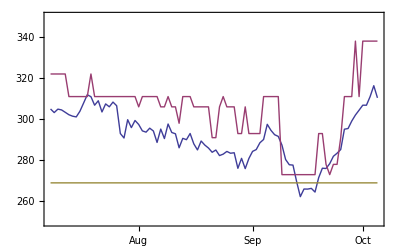

```mathematica
DateListPlot[{Reverse[Take[history[[2]],90]],Reverse[Take[winning,90]],Table[269,{i,90}]},{2008,7,8},Joined->True,PlotStyle->Thick,PlotRange->{Automatic,{250,350}}]
```

```mathematica
natr=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=376101"];
natd=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=409933"];
```

```mathematica
chancend=Take[natd[[All,5]],-300]/(Take[natd[[All,5]],-300]+Take[natr[[All,5]],-300]);
```

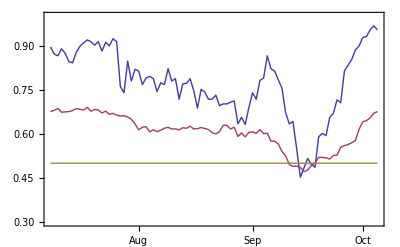

```mathematica
DateListPlot[{Reverse[Take[history[[1]],90]],chancend[[-90;;-1]],Table[.5,{90}]},{2008,7,8},Joined->True,PlotRange->{Automatic,{.3,1}},PlotStyle->Thick]
```

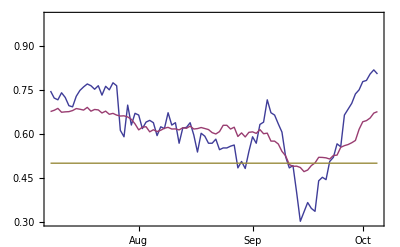

```mathematica
DateListPlot[{Reverse[Take[history[[1]],90]]-.15,chancend[[-90;;-1]],Table[.5,{90}]},{2008,7,8},Joined->True,PlotRange->{Automatic,{.3,1}},PlotStyle->Thick]
```

```mathematica
history
```

{{0.954,0.968,0.954,0.932,0.928,0.9,0.886,0.854,0.834,0.814,0.706,0.716,0.67,0.656,0.594,0.602,0.59,0.486,0.496,0.516,0.484,0.452,0.55,0.642,0.634,0.672,0.756,0.784,0.814,0.822,0.866,0.79,0.782,0.718,0.74,0.69,0.632,0.656,0.634,0.712,0.708,0.702,0.702,0.696,0.732,0.718,0.718,0.742,0.752,0.688,0.746,0.788,0.772,0.77,0.718,0.788,0.78,0.822,0.768,0.774,0.744,0.788,0.796,0.79,0.768,0.814,0.82,0.78,0.848,0.74,0.762,0.914,0.924,0.9,0.912,0.882,0.914,0.902,0.914,0.92,0.91,0.898,0.878,0.842,0.846,0.874,0.89,0.866,0.872,0.896},{310.382,316.296,310.988,306.798,306.808,304.382,302.02,299.088,295.456,295.112,285.232,283.424,281.93,278.334,276.,276.126,271.548,264.516,266.318,265.97,266.004,262.28,269.582,277.648,277.816,280.352,287.37,291.618,292.446,294.574,297.498,290.114,288.518,285.21,284.316,280.882,275.936,280.934,276.08,283.664,283.42,284.302,282.98,282.284,284.99,283.888,285.942,287.4,289.368,285.03,288.,293.022,290.02,290.666,286.064,292.896,293.526,297.65,290.566,295.182,288.68,294.24,295.622,293.69,294.304,297.422,299.362,295.884,299.746,290.842,293.018,306.552,308.322,306.02,307.43,303.52,308.968,306.802,310.944,311.88,307.85,303.862,301.106,301.458,302.164,303.348,304.506,304.89,303.212,304.974}}